```mathematica
Quit[]
```

## Input

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts/FeynArts.m"
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

```mathematica
<<"/home/riccardo/Programs/FormCalc/FormCalc/FormCalc.m"
```

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

```mathematica
Remove[q1]
Remove[q2]
<<"/home/riccardo/Programs/ABISS/ABISS.m"
```

+++++ ABISS` +++++
Version 1.0.0

Amplitudes Builder, Interference Solver and Simplifier

ABISS: A link to the model file SMbgf_Anglerfish.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgf_FARAMIR_general_backup.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgf_FARAMIR_general+SM.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgfQCD_Anglerfish.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgf_TelescopeOctopus_backup.mod has been added to the FeynArts directory

```mathematica
SetPath[NotebookDirectory[]];
```

Define the process:

```mathematica
SetProcess[{V[30]}->{S[30]}];
```

Generate default Input files

```mathematica
GenerateInput[];
```

ABISS Warning: Input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/input/kinematics.m already exist. It will NOT be overwritten.

ABISS Warning: Input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/input/integral_families.m already exist. It will NOT be overwritten.

Import the input files (kinematics + integral families).

```mathematica
ImportInput[];
```

ABISS: Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/input/kinematics.m.

## Diagrams generation

Generate diagrams using feynarts (charged current drell-yan, one loop boxes and born).

```mathematica
SetOptions[InsertFields,  Model -> "SMbgf_Anglerfish", GenericModel ->"Lorentzbgf", InsertionLevel->{Particles}, Restrictions->{NoQuarkMixing}, ExcludeParticles-> {}];
```

```mathematica
process={V[30]}->{S[30]};
```

```mathematica
topologies1L=CreateTopologies[1,1-> 1,ExcludeTopologies->Tadpoles];
```

```mathematica
fields1L=InsertFields[topologies1L, process];
```

loading generic model file /home/riccardo/Programs/FeynArts/FeynArts/Models/Lorentzbgf.gen

> $GenericMixing is OFF

generic model {Lorentzbgf} initialized

loading classes model file /home/riccardo/Programs/FeynArts/FeynArts/Models/SMbgf_Anglerfish.mod

> 60 particles (incl. antiparticles) in 24 classes

> $CounterTerms are ON

> 689 vertices

> 334 counterterms of order 1

> 2 counterterms of order 2

classes model {SMbgf_Anglerfish} initialized

Excluding 24 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 18 Particles insertions

Restoring 24 field point(s)

in total: 18 Particles insertions

```mathematica
amp1L=CreateFeynAmp[fields1L];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 18 Particles amplitudes

in total: 18 Particles amplitudes

> Top. 1 ac/bd/cdcd.m, 0 diagrams

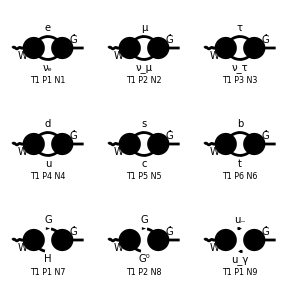

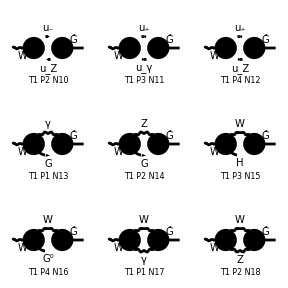

```mathematica
Paint[fields1L];
```

```mathematica
myAmp1L=ExtractAmplitude[amp1L];
```

```mathematica
SaveAmplitudes[myAmp1L,"OneLoopAmplitudes.m"];
```

ABISS: Amplitudes saved in /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/feynArts_amplitudes/OneLoopAmplitudes.m

## Projection and polarization vector

```mathematica
p[Lor1_]:=- I SP[p1,{Lor1}]/SP[p1,p1]
```

### Remove polarization vectors

```mathematica
removePolarizationVectors={PolarizationVector[V[30],p_,i_]->1}
```

{ep[V[30],p_,i_]→1}

## Interference

```mathematica
myAmp1LnoEP=myAmp1L/.removePolarizationVectors;
```

```mathematica
myAmp1LProjection=Map[#*p[Lor1]&,myAmp1LnoEP];
```

```mathematica
myAmp1LnoEP[[1]]
```

-1/(16 π^4)ⅈ FeynAmpDenominator[1/(q1)^2,1/(-ME^2+(q1-k1)^2)] tr[gs[-(q1)],-ⅈ EL gFll ME om_+,ME+gs[-(q1)+k1],ⅈ EL gWlN ga[Lor1].om_-]

```mathematica
myAmp1LProjection[[1]]
```

-1/(16 π^4 SP[p1,p1])FeynAmpDenominator[1/(q1)^2,1/(-ME^2+(q1-k1)^2)] tr[gs[-(q1)],-ⅈ EL gFll ME om_+,ME+gs[-(q1)+k1],ⅈ EL gWlN ga[Lor1].om_-] SP[p1,{Lor1}]

```mathematica
SquareSimplifyAndSave[myAmp1LProjection,{1}]
```

ABISS: Computed contribution 1-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX//interferences/Contribution_1_1.m.

ABISS: Computed contribution 2-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX//interferences/Contribution_2_1.m.

ABISS: Computed contribution 3-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX//interferences/Contribution_3_1.m.

ABISS: Computed contribution 4-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX//interferences/Contribution_4_1.m.

ABISS: Computed contribution 5-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX//interferences/Contribution_5_1.m.

ABISS: Computed contribution 6-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX//interferences/Contribution_6_1.m.

ABISS: Computed contribution 7-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX//interferences/Contribution_7_1.m.

ABISS: Computed contribution 8-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX//interferences/Contribution_8_1.m.

ABISS: Computed contribution 9-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX//interferences/Contribution_9_1.m.

ABISS: Computed contribution 10-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX//interferences/Contribution_10_1.m.

ABISS: Computed contribution 11-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX//interferences/Contribution_11_1.m.

ABISS: Computed contribution 12-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX//interferences/Contribution_12_1.m.

ABISS: Computed contribution 13-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX//interferences/Contribution_13_1.m.

ABISS: Computed contribution 14-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX//interferences/Contribution_14_1.m.

ABISS: Computed contribution 15-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX//interferences/Contribution_15_1.m.

ABISS: Computed contribution 16-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX//interferences/Contribution_16_1.m.

ABISS: Computed contribution 17-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX//interferences/Contribution_17_1.m.

ABISS: Computed contribution 18-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX//interferences/Contribution_18_1.m.

## Shift

```mathematica
ImportInput[];
```

ABISS: Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/input/kinematics.m.

```mathematica
Do[
ShiftAndSave[i,j,False];
,{i,18},{j,1}]
```

ABISS: Integral family {{E0, {me}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_1_1.m.

ABISS: Integral family {{E0, {mm}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_2_1.m.

ABISS: Integral family {{E0, {ml}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_3_1.m.

ABISS: Integral family {{C0, {mu, md}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_4_1.m.

ABISS: Integral family {{C0, {mc, ms}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_5_1.m.

ABISS: Integral family {{C0, {mt, mb}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_6_1.m.

ABISS: Integral family {{C0, {mh, mw}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_7_1.m.

ABISS: Integral family {{C0, {mz, mw}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_8_1.m.

ABISS: Integral family {{E0, {mw}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_9_1.m.

ABISS: Integral family {{C0, {mz, mw}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_10_1.m.

ABISS: Integral family {{E0, {mw}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_11_1.m.

ABISS: Integral family {{C0, {mz, mw}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_12_1.m.

ABISS: Integral family {{D0, {mw}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_13_1.m.

ABISS: Integral family {{C0, {mw, mz}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_14_1.m.

ABISS: Integral family {{C0, {mh, mw}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_15_1.m.

ABISS: Integral family {{C0, {mz, mw}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_16_1.m.

ABISS: Integral family {{E0, {mw}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_17_1.m.

ABISS: Integral family {{C0, {mz, mw}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_18_1.m.

## KiraInput

```mathematica
Do[
GenerateAndSaveKiraInput[i,j];
,{i,18},{j,1}]
```

ABISS: Computed contribution 1-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_1_1.m.

ABISS: Computed contribution 2-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_2_1.m.

ABISS: Computed contribution 3-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_3_1.m.

ABISS: Computed contribution 4-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_4_1.m.

ABISS: Computed contribution 5-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_5_1.m.

ABISS: Computed contribution 6-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_6_1.m.

ABISS: Computed contribution 7-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_7_1.m.

ABISS: Computed contribution 8-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_8_1.m.

ABISS: Computed contribution 9-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_9_1.m.

ABISS: Computed contribution 10-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_10_1.m.

ABISS: Computed contribution 11-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_11_1.m.

ABISS: Computed contribution 12-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_12_1.m.

ABISS: Computed contribution 13-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_13_1.m.

ABISS: Computed contribution 14-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_14_1.m.

ABISS: Computed contribution 15-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_15_1.m.

ABISS: Computed contribution 16-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_16_1.m.

ABISS: Computed contribution 17-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_17_1.m.

ABISS: Computed contribution 18-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_18_1.m.

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[E0,{me},0,1],userIntegral[E0,{me},1,0],userIntegral[E0,{me},1,1],userIntegral[E0,{mm},0,1],userIntegral[E0,{mm},1,0],userIntegral[E0,{mm},1,1],userIntegral[E0,{ml},0,1],userIntegral[E0,{ml},1,0],userIntegral[E0,{ml},1,1],userIntegral[C0,{mu,md},1,1],userIntegral[C0,{mu,md},0,1],userIntegral[C0,{mu,md},1,0],userIntegral[C0,{mc,ms},1,1],userIntegral[C0,{mc,ms},0,1],userIntegral[C0,{mc,ms},1,0],userIntegral[C0,{mt,mb},1,1],userIntegral[C0,{mt,mb},0,1],userIntegral[C0,{mt,mb},1,0],userIntegral[C0,{mh,mw},1,1],userIntegral[C0,{mh,mw},0,1],userIntegral[C0,{mh,mw},1,0],userIntegral[C0,{mz,mw},1,1],userIntegral[C0,{mz,mw},0,1],userIntegral[C0,{mz,mw},1,0],userIntegral[E0,{mw},1,1],userIntegral[E0,{mw},0,1],userIntegral[E0,{mw},1,0],userIntegral[D0,{mw},1,1],userIntegral[C0,{mw,mz},1,1]}

```mathematica
SaveScalarIntegrals["scalar_integrals"];
```

```mathematica
ExportScalarIntegrals["kira_scalar_integrals.dat"];
```

## Apply Kira sub;

```mathematica
ImportScalarIntegrals["scalar_integrals"];
```

```mathematica
ClearRules[]
```

{}

```mathematica
ImportRules[NotebookDirectory[]<>"kira_myintegrals.m"]
```

```mathematica
PrintRules[]
```

{userIntegral[E0,{m1},1,0]→0,userIntegral[E0,{m1},0,1]→userIntegral[B0,{m1},1,0],userIntegral[E0,{m1},1,1]→userIntegral[D0,{m1},1,1],userIntegral[C0,{m1,m2},1,0]→userIntegral[B0,{m1},1,0]}

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[E0,{me},0,1],userIntegral[E0,{me},1,0],userIntegral[E0,{me},1,1],userIntegral[E0,{mm},0,1],userIntegral[E0,{mm},1,0],userIntegral[E0,{mm},1,1],userIntegral[E0,{ml},0,1],userIntegral[E0,{ml},1,0],userIntegral[E0,{ml},1,1],userIntegral[C0,{mu,md},1,1],userIntegral[C0,{mu,md},0,1],userIntegral[C0,{mu,md},1,0],userIntegral[C0,{mc,ms},1,1],userIntegral[C0,{mc,ms},0,1],userIntegral[C0,{mc,ms},1,0],userIntegral[C0,{mt,mb},1,1],userIntegral[C0,{mt,mb},0,1],userIntegral[C0,{mt,mb},1,0],userIntegral[C0,{mh,mw},1,1],userIntegral[C0,{mh,mw},0,1],userIntegral[C0,{mh,mw},1,0],userIntegral[C0,{mz,mw},1,1],userIntegral[C0,{mz,mw},0,1],userIntegral[C0,{mz,mw},1,0],userIntegral[E0,{mw},1,1],userIntegral[E0,{mw},0,1],userIntegral[E0,{mw},1,0],userIntegral[D0,{mw},1,1],userIntegral[C0,{mw,mz},1,1]}

```mathematica
DetermineMasterIntegrals[]
```

```mathematica
PrintMasterIntegrals[]
```

{userIntegral[B0,{me},1,0],userIntegral[D0,{me},1,1],userIntegral[B0,{mm},1,0],userIntegral[D0,{mm},1,1],userIntegral[B0,{ml},1,0],userIntegral[D0,{ml},1,1],userIntegral[C0,{mu,md},1,1],userIntegral[C0,{mu,md},0,1],userIntegral[B0,{mu},1,0],userIntegral[C0,{mc,ms},1,1],userIntegral[C0,{mc,ms},0,1],userIntegral[B0,{mc},1,0],userIntegral[C0,{mt,mb},1,1],userIntegral[C0,{mt,mb},0,1],userIntegral[B0,{mt},1,0],userIntegral[C0,{mh,mw},1,1],userIntegral[C0,{mh,mw},0,1],userIntegral[B0,{mh},1,0],userIntegral[C0,{mz,mw},1,1],userIntegral[C0,{mz,mw},0,1],userIntegral[B0,{mz},1,0],userIntegral[D0,{mw},1,1],userIntegral[B0,{mw},1,0],userIntegral[C0,{mw,mz},1,1]}

```mathematica
Do[
SaveResult[i,j];
,{i,18},{j,1}]
```

## Ward Identity Test

### Total coefficients

```mathematica
diagramCoefficients= {};
Do[diagramCoefficients=Append[diagramCoefficients,<<(NotebookDirectory[]<>"coefficients/Coefficients_"<>ToString[i]<>"_1.m")],{i,18}]
```

```mathematica
diagramCoefficients
```

{{(EL^2 gFll gWlN me^2)/(48 π^4 psq),(EL^2 gFll gWlN (-me^4+me^2 psq))/(48 π^4 psq),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,(EL^2 gFll gWlN mm^2)/(48 π^4 psq),(EL^2 gFll gWlN (-mm^4+mm^2 psq))/(48 π^4 psq),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,(EL^2 gFll gWlN ml^2)/(48 π^4 psq),(EL^2 gFll gWlN (-ml^4+ml^2 psq))/(48 π^4 psq),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,(EL^2 gFud gWdu mu^2 CKM[1,1] CKMC[1,1])/(8 π^4)+(EL^2 gFud gWdu md^2 (-md^2+mu^2+psq) CKM[1,1] CKMC[1,1])/(16 π^4 psq)-(EL^2 gFud gWdu mu^2 (-md^2+mu^2+psq) CKM[1,1] CKMC[1,1])/(16 π^4 psq),(EL^2 gFud gWdu md^2 CKM[1,1] CKMC[1,1])/(16 π^4 psq)-(EL^2 gFud gWdu mu^2 CKM[1,1] CKMC[1,1])/(16 π^4 psq),-(EL^2 gFud gWdu md^2 CKM[1,1] CKMC[1,1])/(16 π^4 psq)+(EL^2 gFud gWdu mu^2 CKM[1,1] CKMC[1,1])/(16 π^4 psq),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,(EL^2 gFud gWdu mc^2 CKM[2,2] CKMC[2,2])/(8 π^4)-(EL^2 gFud gWdu mc^2 (mc^2-ms^2+psq) CKM[2,2] CKMC[2,2])/(16 π^4 psq)+(EL^2 gFud gWdu ms^2 (mc^2-ms^2+psq) CKM[2,2] CKMC[2,2])/(16 π^4 psq),-(EL^2 gFud gWdu mc^2 CKM[2,2] CKMC[2,2])/(16 π^4 psq)+(EL^2 gFud gWdu ms^2 CKM[2,2] CKMC[2,2])/(16 π^4 psq),(EL^2 gFud gWdu mc^2 CKM[2,2] CKMC[2,2])/(16 π^4 psq)-(EL^2 gFud gWdu ms^2 CKM[2,2] CKMC[2,2])/(16 π^4 psq),0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,(EL^2 gFud gWdu mt^2 CKM[3,3] CKMC[3,3])/(8 π^4)+(EL^2 gFud gWdu mb^2 (-mb^2+mt^2+psq) CKM[3,3] CKMC[3,3])/(16 π^4 psq)-(EL^2 gFud gWdu mt^2 (-mb^2+mt^2+psq) CKM[3,3] CKMC[3,3])/(16 π^4 psq),(EL^2 gFud gWdu mb^2 CKM[3,3] CKMC[3,3])/(16 π^4 psq)-(EL^2 gFud gWdu mt^2 CKM[3,3] CKMC[3,3])/(16 π^4 psq),-(EL^2 gFud gWdu mb^2 CKM[3,3] CKMC[3,3])/(16 π^4 psq)+(EL^2 gFud gWdu mt^2 CKM[3,3] CKMC[3,3])/(16 π^4 psq),0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(EL^2 gHFF gHFW mh^2)/(48 π^4)-(EL^2 gHFF gHFW mw^2)/(48 π^4)-(EL^2 gHFF gHFW mh^2 (mh^2-mw^2+psq))/(48 π^4 psq)+(EL^2 gHFF gHFW mw^2 (mh^2-mw^2+psq))/(48 π^4 psq),-(EL^2 gHFF gHFW mh^2)/(48 π^4 psq)+(EL^2 gHFF gHFW mw^2)/(48 π^4 psq),(EL^2 gHFF gHFW mh^2)/(48 π^4 psq)-(EL^2 gHFF gHFW mw^2)/(48 π^4 psq),0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(EL^2 gXFF gXFW)/(48 π^4)+(EL^2 gXFF gXFW (-mw^2+mz^2+psq))/(48 π^4 psq),(EL^2 gXFF gXFW)/(48 π^4 psq),-(EL^2 gXFF gXFW)/(48 π^4 psq),0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(EL^2 gFgagm ggagmW)/(48 π^4)-(EL^2 gFgagm ggagmW (mw^2-psq))/(48 π^4 psq),(EL^2 gFgagm ggagmW)/(48 π^4 psq),0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(EL^2 gFgzgm ggzgmW sw)/(48 π^4)+(EL^2 gFgzgm ggzgmW (mw^2-mz^2-psq) sw)/(48 π^4 psq),-(EL^2 gFgzgm ggzgmW sw)/(48 π^4 psq),(EL^2 gFgzgm ggzgmW sw)/(48 π^4 psq),0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(EL^2 gFgagp ggagpW)/(48 π^4)-(EL^2 gFgagp ggagpW (mw^2-psq))/(48 π^4 psq),(EL^2 gFgagp ggagpW)/(48 π^4 psq),0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(EL^2 gFgzgp ggzgpW sw)/(48 π^4)+(EL^2 gFgzgp ggzgpW (mw^2-mz^2-psq) sw)/(48 π^4 psq),-(EL^2 gFgzgp ggzgpW sw)/(48 π^4 psq),(EL^2 gFgzgp ggzgpW sw)/(48 π^4 psq),0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(EL^2 gFAW gFFA)/(12 π^4),0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(cw^2 EL^2 gFFZ gFZW)/(24 π^4 sw)+(EL^2 gFFZ gFZW sw)/(24 π^4)},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(EL^2 gHFW gHWW)/(24 π^4),0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(EL^2 gXFW gXWW)/(24 π^4),0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(d EL^2 gFAW gWWA)/(48 π^4)-(d EL^2 gFAW gWWA (mw^2-psq))/(48 π^4 psq),(d EL^2 gFAW gWWA)/(48 π^4 psq),0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(d EL^2 gFZW gWWZ sw)/(48 π^4)+(d EL^2 gFZW gWWZ (-mw^2+mz^2+psq) sw)/(48 π^4 psq),(d EL^2 gFZW gWWZ sw)/(48 π^4 psq),-(d EL^2 gFZW gWWZ sw)/(48 π^4 psq),0,0,0}}

```mathematica
coefficients=Plus@@diagramCoefficients
```

{(EL^2 gFll gWlN me^2)/(48 π^4 psq),(EL^2 gFll gWlN (-me^4+me^2 psq))/(48 π^4 psq),(EL^2 gFll gWlN mm^2)/(48 π^4 psq),(EL^2 gFll gWlN (-mm^4+mm^2 psq))/(48 π^4 psq),(EL^2 gFll gWlN ml^2)/(48 π^4 psq),(EL^2 gFll gWlN (-ml^4+ml^2 psq))/(48 π^4 psq),(EL^2 gFud gWdu mu^2 CKM[1,1] CKMC[1,1])/(8 π^4)+(EL^2 gFud gWdu md^2 (-md^2+mu^2+psq) CKM[1,1] CKMC[1,1])/(16 π^4 psq)-(EL^2 gFud gWdu mu^2 (-md^2+mu^2+psq) CKM[1,1] CKMC[1,1])/(16 π^4 psq),(EL^2 gFud gWdu md^2 CKM[1,1] CKMC[1,1])/(16 π^4 psq)-(EL^2 gFud gWdu mu^2 CKM[1,1] CKMC[1,1])/(16 π^4 psq),-(EL^2 gFud gWdu md^2 CKM[1,1] CKMC[1,1])/(16 π^4 psq)+(EL^2 gFud gWdu mu^2 CKM[1,1] CKMC[1,1])/(16 π^4 psq),(EL^2 gFud gWdu mc^2 CKM[2,2] CKMC[2,2])/(8 π^4)-(EL^2 gFud gWdu mc^2 (mc^2-ms^2+psq) CKM[2,2] CKMC[2,2])/(16 π^4 psq)+(EL^2 gFud gWdu ms^2 (mc^2-ms^2+psq) CKM[2,2] CKMC[2,2])/(16 π^4 psq),-(EL^2 gFud gWdu mc^2 CKM[2,2] CKMC[2,2])/(16 π^4 psq)+(EL^2 gFud gWdu ms^2 CKM[2,2] CKMC[2,2])/(16 π^4 psq),(EL^2 gFud gWdu mc^2 CKM[2,2] CKMC[2,2])/(16 π^4 psq)-(EL^2 gFud gWdu ms^2 CKM[2,2] CKMC[2,2])/(16 π^4 psq),(EL^2 gFud gWdu mt^2 CKM[3,3] CKMC[3,3])/(8 π^4)+(EL^2 gFud gWdu mb^2 (-mb^2+mt^2+psq) CKM[3,3] CKMC[3,3])/(16 π^4 psq)-(EL^2 gFud gWdu mt^2 (-mb^2+mt^2+psq) CKM[3,3] CKMC[3,3])/(16 π^4 psq),(EL^2 gFud gWdu mb^2 CKM[3,3] CKMC[3,3])/(16 π^4 psq)-(EL^2 gFud gWdu mt^2 CKM[3,3] CKMC[3,3])/(16 π^4 psq),-(EL^2 gFud gWdu mb^2 CKM[3,3] CKMC[3,3])/(16 π^4 psq)+(EL^2 gFud gWdu mt^2 CKM[3,3] CKMC[3,3])/(16 π^4 psq),-(EL^2 gHFW gHWW)/(24 π^4)+(EL^2 gHFF gHFW mh^2)/(48 π^4)-(EL^2 gHFF gHFW mw^2)/(48 π^4)-(EL^2 gHFF gHFW mh^2 (mh^2-mw^2+psq))/(48 π^4 psq)+(EL^2 gHFF gHFW mw^2 (mh^2-mw^2+psq))/(48 π^4 psq),-(EL^2 gHFF gHFW mh^2)/(48 π^4 psq)+(EL^2 gHFF gHFW mw^2)/(48 π^4 psq),(EL^2 gHFF gHFW mh^2)/(48 π^4 psq)-(EL^2 gHFF gHFW mw^2)/(48 π^4 psq),-(EL^2 gXFF gXFW)/(48 π^4)-(EL^2 gXFW gXWW)/(24 π^4)+(EL^2 gXFF gXFW (-mw^2+mz^2+psq))/(48 π^4 psq)+(EL^2 gFgzgm ggzgmW sw)/(48 π^4)+(EL^2 gFgzgp ggzgpW sw)/(48 π^4)-(d EL^2 gFZW gWWZ sw)/(48 π^4)+(EL^2 gFgzgm ggzgmW (mw^2-mz^2-psq) sw)/(48 π^4 psq)+(EL^2 gFgzgp ggzgpW (mw^2-mz^2-psq) sw)/(48 π^4 psq)+(d EL^2 gFZW gWWZ (-mw^2+mz^2+psq) sw)/(48 π^4 psq),(EL^2 gXFF gXFW)/(48 π^4 psq)-(EL^2 gFgzgm ggzgmW sw)/(48 π^4 psq)-(EL^2 gFgzgp ggzgpW sw)/(48 π^4 psq)+(d EL^2 gFZW gWWZ sw)/(48 π^4 psq),-(EL^2 gXFF gXFW)/(48 π^4 psq)+(EL^2 gFgzgm ggzgmW sw)/(48 π^4 psq)+(EL^2 gFgzgp ggzgpW sw)/(48 π^4 psq)-(d EL^2 gFZW gWWZ sw)/(48 π^4 psq),(EL^2 gFAW gFFA)/(12 π^4)-(EL^2 gFgagm ggagmW)/(48 π^4)-(EL^2 gFgagp ggagpW)/(48 π^4)-(d EL^2 gFAW gWWA)/(48 π^4)-(EL^2 gFgagm ggagmW (mw^2-psq))/(48 π^4 psq)-(EL^2 gFgagp ggagpW (mw^2-psq))/(48 π^4 psq)-(d EL^2 gFAW gWWA (mw^2-psq))/(48 π^4 psq),(EL^2 gFgagm ggagmW)/(48 π^4 psq)+(EL^2 gFgagp ggagpW)/(48 π^4 psq)+(d EL^2 gFAW gWWA)/(48 π^4 psq),-(cw^2 EL^2 gFFZ gFZW)/(24 π^4 sw)+(EL^2 gFFZ gFZW sw)/(24 π^4)}

### Lagrangian parameter replace

```mathematica
<<(NotebookDirectory[]<>"smparameters.m")
parameterReplace=smparameters;
```

```mathematica
coefficients/.parameterReplace//Simplify
```

{(EL^2 me^2)/(96 mw π^4 psq sw^2),(EL^2 (-me^4+me^2 psq))/(96 mw π^4 psq sw^2),(EL^2 mm^2)/(96 mw π^4 psq sw^2),(EL^2 (-mm^4+mm^2 psq))/(96 mw π^4 psq sw^2),(EL^2 ml^2)/(96 mw π^4 psq sw^2),(EL^2 (-ml^4+ml^2 psq))/(96 mw π^4 psq sw^2),(EL^2 (-md^4-mu^4+mu^2 psq+md^2 (2 mu^2+psq)) CKM[1,1] CKMC[1,1])/(32 mw π^4 psq sw^2),(EL^2 (md^2-mu^2) CKM[1,1] CKMC[1,1])/(32 mw π^4 psq sw^2),(EL^2 (-md^2+mu^2) CKM[1,1] CKMC[1,1])/(32 mw π^4 psq sw^2),(EL^2 (-mc^4-ms^4+ms^2 psq+mc^2 (2 ms^2+psq)) CKM[2,2] CKMC[2,2])/(32 mw π^4 psq sw^2),(EL^2 (-mc^2+ms^2) CKM[2,2] CKMC[2,2])/(32 mw π^4 psq sw^2),(EL^2 (mc^2-ms^2) CKM[2,2] CKMC[2,2])/(32 mw π^4 psq sw^2),(EL^2 (-mb^4-mt^4+mt^2 psq+mb^2 (2 mt^2+psq)) CKM[3,3] CKMC[3,3])/(32 mw π^4 psq sw^2),(EL^2 (mb^2-mt^2) CKM[3,3] CKMC[3,3])/(32 mw π^4 psq sw^2),(EL^2 (-mb^2+mt^2) CKM[3,3] CKMC[3,3])/(32 mw π^4 psq sw^2),(EL^2 (mh^4-2 mh^2 mw^2+mw^4-4 mw^2 psq))/(192 mw π^4 psq sw^2),(EL^2 (mh^2-mw^2))/(192 mw π^4 psq sw^2),(EL^2 (-mh^2+mw^2))/(192 mw π^4 psq sw^2),-(EL^2 mw ((mw^2-mz^2) sw^2+4 cw^2 (psq+(-2+d) (mw^2-mz^2) sw^2)))/(192 cw^2 π^4 psq sw^2),((1+4 cw^2 (-2+d)) EL^2 mw)/(192 cw^2 π^4 psq),-((1+4 cw^2 (-2+d)) EL^2 mw)/(192 cw^2 π^4 psq),(EL^2 mw ((-2+d) mw^2-4 psq))/(48 π^4 psq),-((-2+d) EL^2 mw)/(48 π^4 psq),-(EL^2 mw (cw^2-sw^2)^2)/(48 cw^2 π^4 sw^2)}

```mathematica
cfinal=( mw coefficients/.parameterReplace)//Simplify
```

{(EL^2 me^2)/(96 π^4 psq sw^2),(EL^2 (-me^4+me^2 psq))/(96 π^4 psq sw^2),(EL^2 mm^2)/(96 π^4 psq sw^2),(EL^2 (-mm^4+mm^2 psq))/(96 π^4 psq sw^2),(EL^2 ml^2)/(96 π^4 psq sw^2),(EL^2 (-ml^4+ml^2 psq))/(96 π^4 psq sw^2),(EL^2 (-md^4-mu^4+mu^2 psq+md^2 (2 mu^2+psq)) CKM[1,1] CKMC[1,1])/(32 π^4 psq sw^2),(EL^2 (md^2-mu^2) CKM[1,1] CKMC[1,1])/(32 π^4 psq sw^2),(EL^2 (-md^2+mu^2) CKM[1,1] CKMC[1,1])/(32 π^4 psq sw^2),(EL^2 (-mc^4-ms^4+ms^2 psq+mc^2 (2 ms^2+psq)) CKM[2,2] CKMC[2,2])/(32 π^4 psq sw^2),(EL^2 (-mc^2+ms^2) CKM[2,2] CKMC[2,2])/(32 π^4 psq sw^2),(EL^2 (mc^2-ms^2) CKM[2,2] CKMC[2,2])/(32 π^4 psq sw^2),(EL^2 (-mb^4-mt^4+mt^2 psq+mb^2 (2 mt^2+psq)) CKM[3,3] CKMC[3,3])/(32 π^4 psq sw^2),(EL^2 (mb^2-mt^2) CKM[3,3] CKMC[3,3])/(32 π^4 psq sw^2),(EL^2 (-mb^2+mt^2) CKM[3,3] CKMC[3,3])/(32 π^4 psq sw^2),(EL^2 (mh^4-2 mh^2 mw^2+mw^4-4 mw^2 psq))/(192 π^4 psq sw^2),(EL^2 (mh^2-mw^2))/(192 π^4 psq sw^2),(EL^2 (-mh^2+mw^2))/(192 π^4 psq sw^2),-(EL^2 mw^2 ((mw^2-mz^2) sw^2+4 cw^2 (psq+(-2+d) (mw^2-mz^2) sw^2)))/(192 cw^2 π^4 psq sw^2),((1+4 cw^2 (-2+d)) EL^2 mw^2)/(192 cw^2 π^4 psq),-((1+4 cw^2 (-2+d)) EL^2 mw^2)/(192 cw^2 π^4 psq),(EL^2 mw^2 ((-2+d) mw^2-4 psq))/(48 π^4 psq),-((-2+d) EL^2 mw^2)/(48 π^4 psq),-(EL^2 mw^2 (cw^2-sw^2)^2)/(48 cw^2 π^4 sw^2)}

```mathematica
c=cfinal/.{mw->mz cw} //Simplify
```

{(EL^2 me^2)/(96 π^4 psq sw^2),(EL^2 (-me^4+me^2 psq))/(96 π^4 psq sw^2),(EL^2 mm^2)/(96 π^4 psq sw^2),(EL^2 (-mm^4+mm^2 psq))/(96 π^4 psq sw^2),(EL^2 ml^2)/(96 π^4 psq sw^2),(EL^2 (-ml^4+ml^2 psq))/(96 π^4 psq sw^2),(EL^2 (-md^4-mu^4+mu^2 psq+md^2 (2 mu^2+psq)) CKM[1,1] CKMC[1,1])/(32 π^4 psq sw^2),(EL^2 (md^2-mu^2) CKM[1,1] CKMC[1,1])/(32 π^4 psq sw^2),(EL^2 (-md^2+mu^2) CKM[1,1] CKMC[1,1])/(32 π^4 psq sw^2),(EL^2 (-mc^4-ms^4+ms^2 psq+mc^2 (2 ms^2+psq)) CKM[2,2] CKMC[2,2])/(32 π^4 psq sw^2),(EL^2 (-mc^2+ms^2) CKM[2,2] CKMC[2,2])/(32 π^4 psq sw^2),(EL^2 (mc^2-ms^2) CKM[2,2] CKMC[2,2])/(32 π^4 psq sw^2),(EL^2 (-mb^4-mt^4+mt^2 psq+mb^2 (2 mt^2+psq)) CKM[3,3] CKMC[3,3])/(32 π^4 psq sw^2),(EL^2 (mb^2-mt^2) CKM[3,3] CKMC[3,3])/(32 π^4 psq sw^2),(EL^2 (-mb^2+mt^2) CKM[3,3] CKMC[3,3])/(32 π^4 psq sw^2),(EL^2 (mh^4-2 cw^2 mh^2 mz^2+cw^4 mz^4-4 cw^2 mz^2 psq))/(192 π^4 psq sw^2),(EL^2 (mh^2-cw^2 mz^2))/(192 π^4 psq sw^2),-(EL^2 (mh^2-cw^2 mz^2))/(192 π^4 psq sw^2),-(EL^2 mz^2 (-mz^2 sw^2+4 cw^4 (-2+d) mz^2 sw^2+cw^2 (4 psq+(9-4 d) mz^2 sw^2)))/(192 π^4 psq sw^2),((1+4 cw^2 (-2+d)) EL^2 mz^2)/(192 π^4 psq),-((1+4 cw^2 (-2+d)) EL^2 mz^2)/(192 π^4 psq),(cw^2 EL^2 mz^2 (cw^2 (-2+d) mz^2-4 psq))/(48 π^4 psq),-(cw^2 (-2+d) EL^2 mz^2)/(48 π^4 psq),-(EL^2 mz^2 (cw^2-sw^2)^2)/(48 π^4 sw^2)}

```mathematica
PrintMasterIntegrals[]
```

{userIntegral[B0,{me},1,0],userIntegral[D0,{me},1,1],userIntegral[B0,{mm},1,0],userIntegral[D0,{mm},1,1],userIntegral[B0,{ml},1,0],userIntegral[D0,{ml},1,1],userIntegral[C0,{mu,md},1,1],userIntegral[C0,{mu,md},0,1],userIntegral[B0,{mu},1,0],userIntegral[C0,{mc,ms},1,1],userIntegral[C0,{mc,ms},0,1],userIntegral[B0,{mc},1,0],userIntegral[C0,{mt,mb},1,1],userIntegral[C0,{mt,mb},0,1],userIntegral[B0,{mt},1,0],userIntegral[C0,{mh,mw},1,1],userIntegral[C0,{mh,mw},0,1],userIntegral[B0,{mh},1,0],userIntegral[C0,{mz,mw},1,1],userIntegral[C0,{mz,mw},0,1],userIntegral[B0,{mz},1,0],userIntegral[D0,{mw},1,1],userIntegral[B0,{mw},1,0],userIntegral[C0,{mw,mz},1,1]}

```mathematica
m=<<(NotebookDirectory[]<>"coefficients/Masters.m");
```

```mathematica
out=Plus@@(c m)
```

(EL^2 (mc^2-ms^2) CKM[2,2] CKMC[2,2] userIntegral[B0,{mc},1,0])/(32 π^4 psq sw^2)+(EL^2 me^2 userIntegral[B0,{me},1,0])/(96 π^4 psq sw^2)-(EL^2 (mh^2-cw^2 mz^2) userIntegral[B0,{mh},1,0])/(192 π^4 psq sw^2)+(EL^2 ml^2 userIntegral[B0,{ml},1,0])/(96 π^4 psq sw^2)+(EL^2 mm^2 userIntegral[B0,{mm},1,0])/(96 π^4 psq sw^2)+(EL^2 (-mb^2+mt^2) CKM[3,3] CKMC[3,3] userIntegral[B0,{mt},1,0])/(32 π^4 psq sw^2)+(EL^2 (-md^2+mu^2) CKM[1,1] CKMC[1,1] userIntegral[B0,{mu},1,0])/(32 π^4 psq sw^2)-(cw^2 (-2+d) EL^2 mz^2 userIntegral[B0,{mw},1,0])/(48 π^4 psq)-((1+4 cw^2 (-2+d)) EL^2 mz^2 userIntegral[B0,{mz},1,0])/(192 π^4 psq)+(EL^2 (-mc^2+ms^2) CKM[2,2] CKMC[2,2] userIntegral[C0,{mc,ms},0,1])/(32 π^4 psq sw^2)+(EL^2 (-mc^4-ms^4+ms^2 psq+mc^2 (2 ms^2+psq)) CKM[2,2] CKMC[2,2] userIntegral[C0,{mc,ms},1,1])/(32 π^4 psq sw^2)+(EL^2 (mh^2-cw^2 mz^2) userIntegral[C0,{mh,mw},0,1])/(192 π^4 psq sw^2)+(EL^2 (mh^4-2 cw^2 mh^2 mz^2+cw^4 mz^4-4 cw^2 mz^2 psq) userIntegral[C0,{mh,mw},1,1])/(192 π^4 psq sw^2)+(EL^2 (mb^2-mt^2) CKM[3,3] CKMC[3,3] userIntegral[C0,{mt,mb},0,1])/(32 π^4 psq sw^2)+(EL^2 (-mb^4-mt^4+mt^2 psq+mb^2 (2 mt^2+psq)) CKM[3,3] CKMC[3,3] userIntegral[C0,{mt,mb},1,1])/(32 π^4 psq sw^2)+(EL^2 (md^2-mu^2) CKM[1,1] CKMC[1,1] userIntegral[C0,{mu,md},0,1])/(32 π^4 psq sw^2)+(EL^2 (-md^4-mu^4+mu^2 psq+md^2 (2 mu^2+psq)) CKM[1,1] CKMC[1,1] userIntegral[C0,{mu,md},1,1])/(32 π^4 psq sw^2)-(EL^2 mz^2 (cw^2-sw^2)^2 userIntegral[C0,{mw,mz},1,1])/(48 π^4 sw^2)+((1+4 cw^2 (-2+d)) EL^2 mz^2 userIntegral[C0,{mz,mw},0,1])/(192 π^4 psq)-1/(192 π^4 psq sw^2)EL^2 mz^2 (-mz^2 sw^2+4 cw^4 (-2+d) mz^2 sw^2+cw^2 (4 psq+(9-4 d) mz^2 sw^2)) userIntegral[C0,{mz,mw},1,1]+(EL^2 (-me^4+me^2 psq) userIntegral[D0,{me},1,1])/(96 π^4 psq sw^2)+(EL^2 (-ml^4+ml^2 psq) userIntegral[D0,{ml},1,1])/(96 π^4 psq sw^2)+(EL^2 (-mm^4+mm^2 psq) userIntegral[D0,{mm},1,1])/(96 π^4 psq sw^2)+(cw^2 EL^2 mz^2 (cw^2 (-2+d) mz^2-4 psq) userIntegral[D0,{mw},1,1])/(48 π^4 psq)

```mathematica
out>>(NotebookDirectory[]<>"result.m")
```

```mathematica
??Write
```